# Convolution

## ELE 489: Digital Signal Processing Lab

Heath Buchanan / Taylor Brookes

Due: 2/14/23

## Introduction

In this lab we are experimenting with the concept of convolution. Convolution is a mathematical way of combining two signals to form a third. The concept of convolution is used to determine response of a system at rest to an impulse. Because the systems we use are designed to operate in their linear regions, we can use the principles of linearity and superposition to calculate these responses. As we take increasing amounts of discrete unit impulses, or a unit step, we see that our output will resemble a continuous input. Our code implements this procedure with two lists in Problem One. For Problem Two, we will convolve two signals and create graphs to compare the input and output signals. Finally, in Problem Three, we compare the time it takes for our code to run compared to the ListConvolve function embedded in the Wolfram Language.

## Problem 1. Code Development

Implement the convolution sum directly form the defining formula using structural programming constructs such as nested Do or For loops only. The resulting implementation is know as the linear or direct form and commonly used when convolution is programmed on general purpose computers.

The convolution formula is as follows:

y_n =∑_(k=1)^N h_k x_(n-k+1)   for n = 1, ...., M.

```mathematica
x  := {19,7,4,16,9,14,19,11};
h := {17,19,19};
```

Directly above, we have defined a list of variables for x and h. The code below implements a user-defined function to compute the convolution of x and h using numerical iteration of the flip and slide method. In order to index correctly for existing samples only, we test solutions in our nested For loop between the length of lists x and h. The solution list, called table, is a table of steady-state values developed by multiplying each value of h by the loop defined indexed value(s) of  x and summing the products where applicable.

Here is an example of one convolution sum:
y_3 =h_1 x_3+h_2 x_2+h_3 x_1

Here is an overview of what each variable of the method does:
lenX = length of list “x”
lenH = length of list “h”
table = initializes a list of length (lenX - lenH+1), filled with 0’s, to store the steady-state values of the convolution function
i =  index that starts at 1 and increases until it reaches the last value in the list ”h” (lenH); this is the sub value of h_1.
k = index that starts at “l” and decreases until it reaches (l - lenH + 1); this is the sub value of x_3.
l = index that starts at the first steady-state value (lenH) and goes until the final steady-state value (lenX). This is the sub value of y_3.
m = the same value as i, but with a different meaning. It is an index that starts at 1 and increases until it reaches (lenH); this value represents the amount of summations to do for the y_3 calculation. For example, m = 3 for y_3= h_1 x_3+h_2 x_2+h_3 x_1.
total = the y_3 value. this value is added to the (l - lenH + 1) index of the table. y_3 would be index 1.

```mathematica
convolve[x_,h_] := Module[{lenX,lenH,table,i,k,l,m,total},
lenX =  Length [x];
lenH = Length[h];
table = Table[0, {lenX-lenH+1}];
For[l = lenH, l<=lenX,l++,i = 1; k=l;total = 0;
For[m = 1, m <=lenH, m++,total +=h[[m]]*x[[k]]; k--; i++];
table [[l-lenH+1]]= total
]
;table]
convolve[x,h]
```

{562,481,533,713,760,814}

```mathematica
ListConvolve[h,x]
```

{562,481,533,713,760,814}

```mathematica
{562,481,533,713,760,814}
```

{562,481,533,713,760,814}

## Problem 2. Code Testing

(a). Convolve with the following sequence

```mathematica
ha=Table[1/11.,{11}];
```

```mathematica
ListLinePlot[{Labeled[twave, "original twave"],Labeled[convolve[twave,ha], "convolution with ha"]}, PlotLayout -> "Row"]
```

-Graphics-

As we can see, convolving twave with ha gives us a rounded average of our original twave.

```mathematica
ListLinePlot[{Labeled[twaveN, "original twaveN"],Labeled[convolve[twaveN,ha], "convolution with ha"]}, PlotLayout -> "Row"]
```

-Graphics-

Similar to the previous step, convolving twaveN with ha also gives us a smoothed-out average of the original signal.

(b). Convolve the following sequence

```mathematica
hb={0.021614906829088183,0.04395541408652306,0.07787783685983768,0.1187181374719673,0.15385744484189667,0.16795251982137419,0.15385744484189667,0.1187181374719673,0.07787783685983768,0.04395541408652306,0.021614906829088183};
```

```mathematica
ListLinePlot[{Labeled[twave, "original twave"],Labeled[convolve[twave,hb], "convolution with hb"]}, PlotLayout -> "Row"]
```

-Graphics-

Convolving our original twave function with hb gave us a more precise average than we received by convolving with ha.

```mathematica
ListLinePlot[convolve[twaveN, hb]];
ListLinePlot[{Labeled[twaveN, "original twaveN"],Labeled[convolve[twaveN,hb], "convolution with hb"]}, PlotLayout -> "Row"]
```

-Graphics-

Again we see that convolving the original twaveN with the list hb gives us a more precise averaging of the signal than we got by convolving with ha.

(c). Convolve the following sequence:

```mathematica
hc=100{-0.006311233955184732,0.01999672357296892,-0.012871592754918868,-0.021605858826443274,0.03438101889232266,0.06853499469894078,0.,-0.06853499469894078,-0.03438101889232266,0.021605858826443274,0.012871592754918868,-0.01999672357296892,0.006311233955184732};
```

```mathematica
ListLinePlot[{Labeled[twave, "original twave"],Labeled[convolve[twave,hc], "convolution with hc"]}, PlotLayout -> "Row"]
```

-Graphics-

When we convolve the triangle twave with hc, our result is a square wave with overshoot and undershoot on the edges due to the quality of approximating the resulting signal. More samples would give us a reduction in over/under shoots.

```mathematica
ListLinePlot[{Labeled[twaveN, "original twaveN"],Labeled[convolve[twaveN,hc], "convolution with hc"]}, PlotLayout -> "Row"]
```

-Graphics-

Since the original twaveN is a highly distorted triangle wave, convolving it with hc gives us an even more distorted response due again to the quality of approximating the signal.

## Problem 3. Code Timing

Compare the timing of your convolve function with the built-in ListConvolve function.

Setting up the lists h and x:

```mathematica
h = {1,1,1}/3.;
```

```mathematica
x = RandomReal[{0,1},1000];
```

Use RepeatedTiming to measure the evaluation time of the ListConvolve function

```mathematica
a1 =RepeatedTiming[ListConvolve[h,x];][[1]]
```

0.0000222881

```mathematica
b1 = RepeatedTiming[convolve[x,h];][[1]]
```

0.012224

Change the length of x:

```mathematica
x = RandomReal[{0,1},10000];
```

Compare the times:

```mathematica
a2 = RepeatedTiming[ListConvolve[h,x];][[1]]
```

0.000162146

```mathematica
b2 = RepeatedTiming[convolve[x,h];][[1]]
```

0.108917

Increasing the length of the list to 100k

```mathematica
x = RandomReal[{0,1},100000];
```

```mathematica
a3 =RepeatedTiming[ListConvolve[h,x];][[1]]
```

0.00149437

```mathematica
b3 = RepeatedTiming[convolve[x,h];][[1]]
```

1.20652

As we can see, the ListConvolve function is approximately 3 orders of magnitude faster than our convolve method.

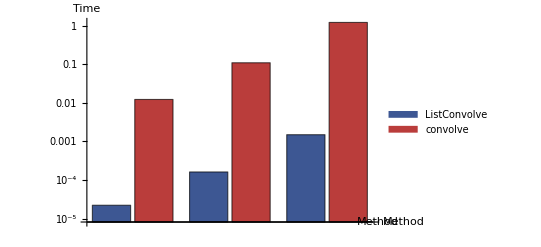

```mathematica
BarChart[{{a1,b1},{a2,b2},{a3,b3}}, ChartLegends-> {"ListConvolve","convolve"}, ChartStyle->"DarkRainbow", ScalingFunctions->"Log", Axes->True, AxesLabel->{"Method","Time"}]
```

## Conclusion

Convolution is a mathematical operation that is used in the analysis and design of signals and systems. It is used to determine the output of a system when a particular input is applied. The convolution theorem states that the convolution of two signals in the time domain is equivalent to the product of their Fourier transforms in the frequency domain. This theorem allows us to analyze the response of linear systems to inputs such as unit step and unit impulse.
	Our results show convolutions attempt to plot the input function in response to the original signal and show how the output changes as a result. In problem 2 part a), when repeated identical input values are applied, we see that the signal is smoothed out and reduces the noise of the original signal. An increasing and then decreasing input signal in problem 2 part b) outputs the same result, but with more noise than before. In response to an input of alternating positive and negative values (a twave for the input function) in problem 2 part c), we received an output of an H-shaped signal in the first part and the twave signal with much more noise in the second plot. This is because, in the first plot, the input values are very similar to the original signal of the twave, which attempts to create an output of either a consistent positive value or a consistent negative value. The second plot with noise distorts the input signal enough that the input values do not align nicely with the original signal, causing additional noise.
	In problem 3, we see that our convolution function is slower than the built-in convolution function in Mathematica. This can be attributed to many reasons, such as machine code optimization. Our results show that our function is 100-1000x slower than the built-in function.